## Exercícios referentes à sec. 2.4 - “Our Universe”, Cosmology, D. Baumann

Dimas Jackson de Oliveira

#### 1) Cálculo da idade do universo

i) Universo dominado por energia escura
Definindo os parâmetros (H0 em 1/segundo):

```mathematica
Ωr=9*10^(-5);Ωm=0.31;ΩΛ=1-Ωm-Ωr;H0=68/(3*10^19);
```

A idade do universo em segundos é dada por

```mathematica
t0=N[1/H0*∫_0^1 1/(√(Ωr*a^(-2)+Ωm*a^(-1)+ΩΛ*a^2))ⅆa]
```

4.21277×10^17

Convertendo para anos:

```mathematica
t0=t0/(60*60*24*365.25)
```

1.33495×10^10

ii) Universo dominado por matéria
Definindo os parâmetros (H0 em 1/segundo):

```mathematica
Ωr=9*10^(-5);Ωm=1-Ωr;ΩΛ=0;H0=68/(3*10^19);
```

A idade do universo em segundos é dada por

```mathematica
t0=N[1/H0*∫_0^1 1/(√(Ωr*a^(-2)+Ωm*a^(-1)+ΩΛ*a^2))ⅆa]
```

2.94092×10^17

Convertendo para anos:

```mathematica
t0=t0/(60*60*24*365.25)
```

9.3192×10^9

#### 2) Cálculo da equivalência matéria-radiação

```mathematica
Clear["Global`*"]
```

Das equações de Friedmann obtêm-se o fator de escala para a equivalência matéria-radiação

```mathematica
s=Solve[Ωm*a^(-3)==Ωr*a^(-4),a]
```

{{a→Ωr/Ωm}}

Definindo os parâmetros (H0 em 1/segundo):

```mathematica
Ωr=9*10^(-5);Ωm=0.31;ΩΛ=1-Ωm-Ωr;H0=68/(3*10^19);
```

```mathematica
aeq=s[[1]][[1]][[2]]
```

0.000290323

Tempo de equivalência:

```mathematica
teq=N[1/H0*∫_0^aeq 1/(√(Ωr*a^(-2)+Ωm*a^(-1)+ΩΛ*a^2))ⅆa]
```

1.53074×10^12

Convertendo para anos:

```mathematica
teq=teq/(60*60*24*365.25)
```

48506.1

Redshift de equivalência:

```mathematica
zeq=Solve[aeq==1/(1+z),z][[1]][[1]][[2]]
```

3443.44

#### 3) Cálculo da equivalência matéria-energia escura

```mathematica
Clear["Global`*"]
```

Das equações de Friedmann obtêm-se o fator de escala para a equivalência matéria-energia escura

```mathematica
s=Solve[Ωm*a^(-3)==ΩΛ,a][[1]][[1]]
```

a→Ωm^(1/3)/ΩΛ^(1/3)

Definindo os parâmetros (H0 em 1/segundo):

```mathematica
Ωr=9*10^(-5);Ωm=0.31;ΩΛ=1-Ωm-Ωr;H0=68/(3*10^19);
```

```mathematica
amΛ=s[[2]]
```

0.765931

Tempo de equivalência:

```mathematica
tmΛ=N[1/H0*∫_0^amΛ 1/(√(Ωr*a^(-2)+Ωm*a^(-1)+ΩΛ*a^2))ⅆa]
```

3.11924×10^17

Convertendo para anos:

```mathematica
tmΛ=tmΛ/(60*60*24*365.25)
```

9.88428×10^9

Redshift de equivalência:

```mathematica
zmΛ=Solve[amΛ==1/(1+z),z][[1]][[1]][[2]]
```

0.3056

#### 4) Gráfico da densidade em função do redshift

```mathematica
Clear["Global`*"]
```

Definindo o parâmetro de densidade Ω para cada caso:

```mathematica
Ω0r=9*10^(-5);Ω0m=0.31;Ω0Λ=1-Ω0m-Ω0r;H0=68/(3*10^19);
```

```mathematica
Ωm[z_]:=Ω0m*(1/(1+z))^(-3);
Ωr[z_]:=Ω0r*(1/(1+z))^(-4);
ΩΛ[z_]:=Ω0Λ;
```

Gráfico do parâmetro de densidade em função do redshift mostrando o ponto em que a energia escura passa a dominar sobre a matéria (z em escala logarítimica):

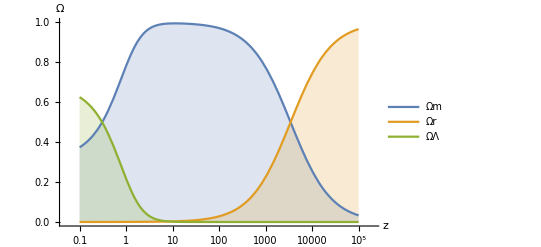

```mathematica
LogLinearPlot[{Ωm[z]/(Ωm[z]+Ωr[z]+ΩΛ[z]),Ωr[z]/(Ωm[z]+Ωr[z]+ΩΛ[z]),ΩΛ[z]/(Ωm[z]+Ωr[z]+ΩΛ[z])},{z,10^-1,100000},PlotLegends->{"Ωm","Ωr","ΩΛ"},AxesLabel->{"z","Ω"},LabelStyle->{Black,12},PlotStyle->Thick,PlotRange->{0,1},Filling->Axis]
```

#### 5) Gráfico da distância de luminosidade em função do redshift

Definindo a distância de luminosidade:

```mathematica
dH=3*10^8/H0;
Do[f[z]=NIntegrate[1/√(Ω0r(1+u)^4+Ω0m(1+u)^3+Ω0Λ),{u,0,z}],{z,0,2,0.01}]
dL=Table[{z,5Log10[dH(1+z)*f[z]/(3*10^22)]+25},{z,0,2,0.01}];
Do[f[z]=NIntegrate[1/√(Ω0r(1+u)^4+Ω0m(1+u)^3),{u,0,z}],{z,0,2,0.01}]
dL2=Table[{z,5Log10[dH(1+z)*f[z]/(3*10^22)]+25},{z,0,2,0.01}];
```

Gráfico comparando a distância de luminosidade para o universo com a constante cosmológica ou sem a constante cosmológica:

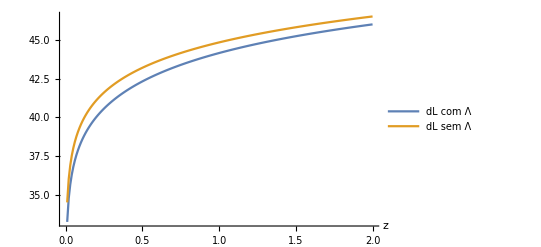

```mathematica
ListLinePlot[{dL,dL2},AxesLabel->{"z",""},LabelStyle->{Black,12},PlotLegends->{"dL com Λ","dL sem Λ"}]
```